```mathematica
(* Convergence of Fourier Series to a function depending on number of terms*)
```

```mathematica
NScProd[f_,g_] := (1/(2*Pi)) *NIntegrate[f Conjugate[g],{x,-Pi,Pi}];
NFcoef[f_,n_] := Table[NScProd[f,Exp[ ⅈ k x]],{k,-n,n}];
cf[f_,n_] = Chop[NFcoef[f,n]]
fct[c_,k_] := (k-1-(Length[c]-1)/2);
Fseries[c_] := Sum[c[[k]]Exp[ⅈ fct[c,k] x],{k,1,Length[c]}];


FConvPlot[f_,n_] := Module[{c,F,plt},
c = NFcoef[f,n];
F = Fseries[c];
plt = Plot[{F,f},{x,-π,π},Frame->True,GridLines->Automatic,PlotStyle->{Red,Blue},PlotLabel->"Convergence of Fourier Series"];


Return[plt]
]
```

```mathematica
(* Functions to evaluate *)
f5[x_] := 1+Sin[x]+10Cos[x]+100Sin[2x]+1000Cos[3x];
p1[x_] := x - Floor[(x+Pi) / (2*Pi)] (2Pi);
f1[x_] := If[p1[x]<0,0,1];
f3[x_]:=Abs[Cos[x/2]];
f4[x_]:=2 Sin[Cos[x]]+3 Cos[Sin[x]];
```

```mathematica
(* 1: Heaviside Function *)
```

```mathematica
Manipulate[FConvPlot[f1[x],k],{k,1,20,2}]

Off[NIntegrate::slwcon,NIntegrate::ncvb];
```

```mathematica
(* Notice Gibbs' Phenomenon at large k*)
```

```mathematica
(* 2: Simple Periodic Function *)
Manipulate[FConvPlot[f5[x],k],{k,1,4,1}]
```

```mathematica
(* Converges perfectly even at small k, since our function is a smooth periodic*)
```

```mathematica
(* 3: Simple Polynomial *)
```

```mathematica
f9[x_] = (x-1)(x-1/3)(x+2/3)(x+2)(x-3);
Manipulate[FConvPlot[f9[x],k],{k,1,50,2}]
```

```mathematica
(* Will not converge for a non-periodic function. With a large number of coefficients, models may approach convergence for a small interval, but not for the entire function, as seen below. *)
```

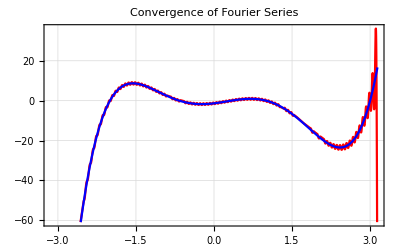

```mathematica
FConvPlot[f9[x],100]
```

```mathematica
(* 4: Complex Construction of Periodic Functions*)
f6[x_] := f4[x]+f3[f5[x]];
```

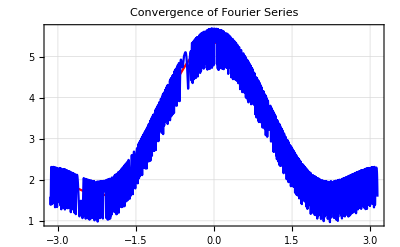

```mathematica
FConvPlot[f6[x],3]
```

```mathematica
(* Note this function is periodic, but we are only displaying one period. Fourier series will eventually converge to f6, but with a great number of terms and taking a long time to compute*)
```

```mathematica
(* 5: Non-Periodic Function*)
```

```mathematica
f7[x_] := Exp[0.5x]*Sin[10x];
Manipulate[FConvPlot[f7[x],k],{k,1,50,2}]
```

```mathematica
(* Again, will not converge for a non-periodic function. As we can see here, we can come much closer to convergence with a large number of terms, but we will never converge over the entire function. *)
```

```mathematica
(* 6: Linear Function *)
```

```mathematica
Manipulate[FConvPlot[x+10,k],{k,1,50,2}]
```

```mathematica
(* Even an incredibly simple function like y= x+10, we cannot create complete convergence as it is not periodic.*)
```